## Basic linear regression

```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/mma_lessons/code

```mathematica
data=Table[{x,x^2+2 x-1+RandomReal[{0,0.5}]},{x,-2,2,0.1}]
```

{{-2.,-0.757003},{-1.9,-0.791409},{-1.8,-0.90949},{-1.7,-1.23008},{-1.6,-1.32396},{-1.5,-1.40511},{-1.4,-1.6124},{-1.3,-1.6868},{-1.2,-1.77325},{-1.1,-1.80387},{-1.,-1.55337},{-0.9,-1.77734},{-0.8,-1.58636},{-0.7,-1.51849},{-0.6,-1.60605},{-0.5,-1.41878},{-0.4,-1.34802},{-0.3,-1.2305},{-0.2,-1.21218},{-0.1,-0.83845},{0.,-0.61567},{0.1,-0.390582},{0.2,-0.122314},{0.3,-0.159171},{0.4,-0.0167738},{0.5,0.455068},{0.6,1.02441},{0.7,1.26696},{0.8,1.54362},{0.9,1.8535},{1.,2.20931},{1.1,2.89468},{1.2,3.09106},{1.3,3.62116},{1.4,3.94676},{1.5,4.37593},{1.6,4.84073},{1.7,5.49423},{1.8,5.9943},{1.9,6.58742},{2.,7.03873}}

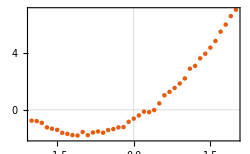

```mathematica
plotData=ListPlot[data,PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,7}},ImageSize->250]
```

```mathematica
Export["pics/08-fit-plot-data.pdf",plotData]
```

pics/08-fit-plot-data.pdf

```mathematica
model1=Fit[data, {1,x},x]
```

0.671962+1.96532 x

```mathematica
model2=Fit[data, {1,x,x^2},x]
```

-0.69666+1.96532 x+0.977587 x^2

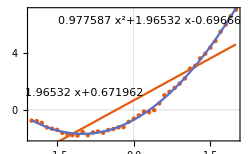

```mathematica
plotDataFit=Show[
ListPlot[data,PlotRange->{{-2,2},{-2,7}}], 
Plot[{model1,model2}, {x, -2, 2},
PlotLabels->Placed[
{Framed[model1],Framed[model2]},
{{-0.75,0.15},{1,5.15}}]],
ImageSize->250, PlotTheme->"Scientific"
]
```

```mathematica
Export["pics/08-fit-plot-data-fit.pdf",plotDataFit]
```

pics/08-fit-plot-data-fit.pdf

## Information about the model

```mathematica
lm=LinearModelFit[data,{1,x,x^2},x]
```

FittedModel[-0.772289+1.99258 x+0.993674 x^2]

```mathematica
lm//Normal
```

-0.772289+1.99258 x+0.993674 x^2

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

## Predict

```mathematica
data
```

{{-2.,-0.841622},{-1.9,-1.18141},{-1.8,-1.27026},{-1.7,-1.18113},{-1.6,-1.51716},{-1.5,-1.34568},{-1.4,-1.52718},{-1.3,-1.51766},{-1.2,-1.50226},{-1.1,-1.71597},{-1.,-1.86866},{-0.9,-1.98263},{-0.8,-1.47193},{-0.7,-1.90936},{-0.6,-1.42165},{-0.5,-1.59565},{-0.4,-1.32428},{-0.3,-1.39204},{-0.2,-0.986159},{-0.1,-0.774483},{0.,-0.834813},{0.1,-0.700034},{0.2,-0.494794},{0.3,0.092168},{0.4,0.0384816},{0.5,0.361005},{0.6,0.650006},{0.7,0.990222},{0.8,1.31525},{0.9,2.07639},{1.,2.0467},{1.1,2.48245},{1.2,3.17412},{1.3,3.76094},{1.4,4.02777},{1.5,4.46522},{1.6,4.82047},{1.7,5.71989},{1.8,5.91719},{1.9,6.77257},{2.,7.01898}}

```mathematica
rules=Apply[Rule,data,2]
```

{-2.→-0.841622,-1.9→-1.18141,-1.8→-1.27026,-1.7→-1.18113,-1.6→-1.51716,-1.5→-1.34568,-1.4→-1.52718,-1.3→-1.51766,-1.2→-1.50226,-1.1→-1.71597,-1.→-1.86866,-0.9→-1.98263,-0.8→-1.47193,-0.7→-1.90936,-0.6→-1.42165,-0.5→-1.59565,-0.4→-1.32428,-0.3→-1.39204,-0.2→-0.986159,-0.1→-0.774483,0.→-0.834813,0.1→-0.700034,0.2→-0.494794,0.3→0.092168,0.4→0.0384816,0.5→0.361005,0.6→0.650006,0.7→0.990222,0.8→1.31525,0.9→2.07639,1.→2.0467,1.1→2.48245,1.2→3.17412,1.3→3.76094,1.4→4.02777,1.5→4.46522,1.6→4.82047,1.7→5.71989,1.8→5.91719,1.9→6.77257,2.→7.01898}

```mathematica
Predict[rules]
```

PredictorFunction[…]

```mathematica
knn=Predict[rules,Method->{"NearestNeighbors","NeighborsNumber"->2}]
```

PredictorFunction[…]

```mathematica
rf = Predict[rules,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
nn = Predict[rules,Method->"NeuralNetwork"]
```

PredictorFunction[…]

```mathematica
predict = Predict[rules]
```

PredictorFunction[…]

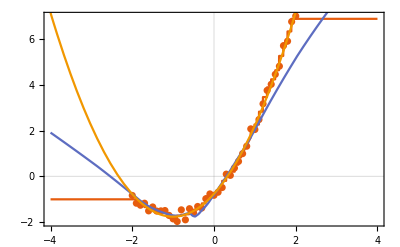

```mathematica
plotDataFitPreict=Show[
ListPlot[data,PlotRange->{{-4,4},{-2,7}}], 
Plot[{knn[x],nn[x],model2}, {x, -4, 4}]
]
```

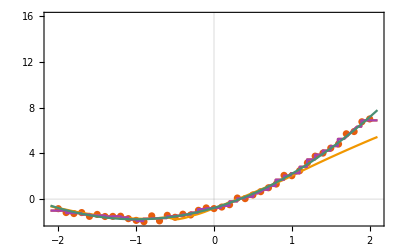

```mathematica
plotDataFitPreictGeneral=Show[
ListPlot[data,PlotRange->{{-2.1,2.1},{-2,16}}], 
Plot[{knn[x],dt[x],nn[x],predict[x],model2}, {x, -2.1, 2.1}]
]
```

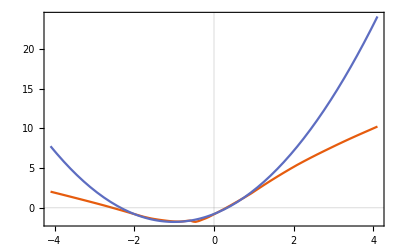

```mathematica
Plot[{nn[x],model2}, {x, -4.1, 4.1}]
```

```mathematica
testSet = Flatten[Table[{x->x^2},{x,-10,5,0.2}]]
```

{-10.→100.,-9.8→96.04,-9.6→92.16,-9.4→88.36,-9.2→84.64,-9.→81.,-8.8→77.44,-8.6→73.96,-8.4→70.56,-8.2→67.24,-8.→64.,-7.8→60.84,-7.6→57.76,-7.4→54.76,-7.2→51.84,-7.→49.,-6.8→46.24,-6.6→43.56,-6.4→40.96,-6.2→38.44,-6.→36.,-5.8→33.64,-5.6→31.36,-5.4→29.16,-5.2→27.04,-5.→25.,-4.8→23.04,-4.6→21.16,-4.4→19.36,-4.2→17.64,-4.→16.,-3.8→14.44,-3.6→12.96,-3.4→11.56,-3.2→10.24,-3.→9.,-2.8→7.84,-2.6→6.76,-2.4→5.76,-2.2→4.84,-2.→4.,-1.8→3.24,-1.6→2.56,-1.4→1.96,-1.2→1.44,-1.→1.,-0.8→0.64,-0.6→0.36,-0.4→0.16,-0.2→0.04,0.→0.,0.2→0.04,0.4→0.16,0.6→0.36,0.8→0.64,1.→1.,1.2→1.44,1.4→1.96,1.6→2.56,1.8→3.24,2.→4.,2.2→4.84,2.4→5.76,2.6→6.76,2.8→7.84,3.→9.,3.2→10.24,3.4→11.56,3.6→12.96,3.8→14.44,4.→16.,4.2→17.64,4.4→19.36,4.6→21.16,4.8→23.04,5.→25.}

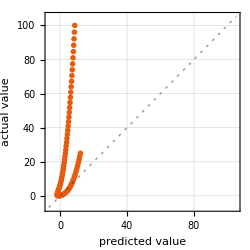
Predictor Measurements
Predictor method | NeuralNetwork
Number of test examples | 76
Standard deviation | 33.6 ± 3.5
Standard deviation baseline | 27.9 ± 2.4
R-squared | -0.454 ± 0.39
Mean cross entropy | 703. ± 150.
Single evaluation time | 2.97 ms/example
Batch evaluation speed | 961. examples/s
-Graphics- |

```mathematica
PredictorMeasurements[nn, testSet]
```